## Distributed Consensus Problem -- Testing & Notes

From: https://writings.stephenwolfram.com/2021/05/the-problem-of-distributed-consensus/

#### From The Webpage:

#### Hypothesis: The initial system consists of cells with a certain fraction of 3 distinct colours. There exists some rule, of which when applied to the system, will turn all the cells to the majority colour when that fraction of the colours exceeds a certain threshold.

## A simple Distributive Consensus problem

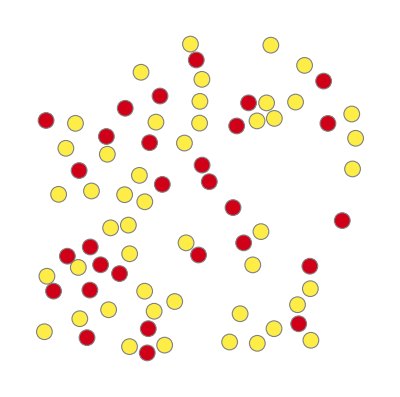

```mathematica
BlockRandom[SeedRandom[77]; (*create randomly 77 seeds*)
Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.10,2,2],Rectangle[{0,0},{40,40}]]["Points"],clrs}, (*setting the points parameters*)clrs=Table[RandomChoice[{.65,.35}->{Hue[0.15,0.72,1],Hue[0.98,1,0.8200000000000001]}],Length[pts]]; (*represents a color in the HSB color space with hue h, saturation & brightness*)
Graphics[{EdgeForm[Gray],Table[Style[Disk[pts[[n]]],clrs[[n]]],{n,Range[Length[pts]]}]}]]]
(*showing the Graphics from the parameters above*)
```

to efficiently find the most common colour among the nodes / finding the majority of the colour: 
First connect each node to some number of neighbors, picking the neighbors according to the spatial layout of the nodes:

```mathematica
ConsensusState[points_, colors_, nn_ : 5] := 
 NearestNeighborGraph[points, nn, DirectedEdges -> True, 
  DistanceFunction -> EuclideanDistance, 
  VertexStyle -> MapThread[Rule, {points, colors}], 
  VertexSize -> 0.75, EdgeStyle -> Blue]; 
(*above defines a function*)

BlockRandom[SeedRandom[77]; 
 Module[{pts = 
    RandomPointConfiguration[HardcorePointProcess[0.09, 2, 2], 
      Rectangle[{0, 0}, {40, 40}]]["Points"], clrs},
  clrs = 
   Table[
    RandomChoice[{.65, .35} -> {Hue[0.15, 0.72, 1], Hue[
       0.98, 1, 0.8200000000000001]}], Length[pts]]; 
  ConsensusState[pts, clrs]]]
```

-Graphics-

at each step updating the color of each node to be whatever the “majority color” of its neighbors is 
--> 	converges after a few steps to make all nodes have the “majority color” (which here is yellow)—or in effect 	“agree” on what the majority color is:

```mathematica
ConsensusState[points_,colors_,nn_:5]:=NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance,VertexStyle->MapThread[Rule,{points,colors}],VertexSize->0.75,EdgeStyle->Gray]
NodeDependencies[points_,nn_:5]:=Table[n->Flatten[Map[Position[points,#]&,VertexOutComponent[NearestNeighborGraph[points,nn,DirectedEdges->True,DistanceFunction->EuclideanDistance],points[[n]],{1}]]],{n,Range[Length[points]]}]
SynchronousStepNewColors[dependencies_,colors_]:=Flatten[Map[With[{neighbors=Sort[Counts[Part[colors,Last[#]]],Greater]},If[DuplicateFreeQ[Values[neighbors]],First[Keys[neighbors]],colors[[First[#]]]]]&,dependencies]]
GraphicsGrid[Partition[BlockRandom[SeedRandom[77];Module[{pts=RandomPointConfiguration[HardcorePointProcess[0.09,2,2],Rectangle[{0,0},{40,40}]]["Points"],clrslist,highlights},clrslist=NestList[SynchronousStepNewColors[NodeDependencies[pts],#]&,Table[RandomChoice[{.65,.35}->{Yellow,Red}],Length[pts]],7];
MapIndexed[With[{colors=#},Graph[ConsensusState[pts,colors],ImageSize->150]]&,clrslist]]],4],ImageSize->600]
```

-Graphics-

#### Next: Background & Deterministic Cellular Automata

synthesizing reliable systems out of unreliable components; 
in certain cases there can be a “phase transition” so that below a certain “temperature” there can be zero effect on the consensus output—implying robustness to a certain level of noise;
graph cellular automaton: the connections between elements are defined by a graph, but the updates are all done synchronously at each step.

#### 1D deterministic cellular automata:

We have a line of cells, each with one of two possible colors. Then we update the colors of these cells in a sequence of steps, based on a local rule which depends on neighboring cells.;
main idea: We want all the cells to turn red if p > 1/2, and all of them to turn yellow if p < 1 / 2 . The most obvious rule that might achieve this would just replace each cell by the majority color in its neighborhood (rule 232)

```mathematica
RulePlot[CellularAutomaton[433],ColorRules->{0-> Yellow,1->Red, 2-> Blue},MeshStyle->Orange]
```

RulePlot[CellularAutomaton[433],ColorRules→{0→RGBColor[1, 1, 0],1→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1]},MeshStyle→RGBColor[1, 0.5, 0]]

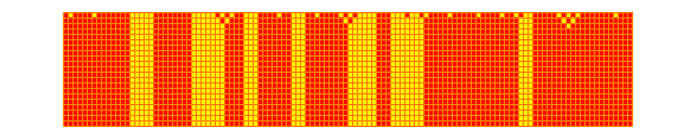

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[232,RandomChoice[{.6,.4}->{1,0},120],20],Mesh->True,ColorRules->{0->Yellow,1->Red},MeshStyle->Orange]]
```

#### A rule for a 1D deterministic cellular automation which leads to global consensus (or solving the “density classification problem” of deciding whether the density of initial red cells is above or below 50%) "radius 3" rule (operating on size - 7 neighborhoods) was constructed ("GKL rule") : {l3_, _, l1_, c_, r1_, _, r3_} :> If[If[c == 0, r1 + r3, l1 + l3] + c >= 2, 1, 0]

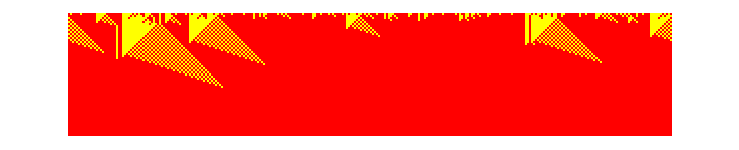

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0-> Yellow ,1->Red},Frame->False]]
```

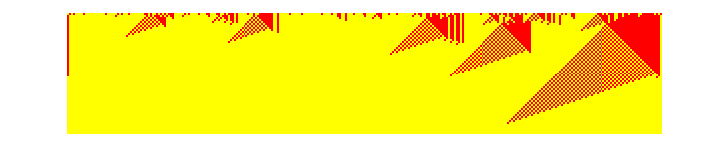

```mathematica
BlockRandom[SeedRandom[569];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.4,.6}->{1,0},300],60],ColorRules->{0->Yellow,1-> Red},Frame->False]]
```

```mathematica
data=ParallelTable[If[p==.5,Nothing,MeanAround/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{p,1-p}->{1,0},5000],200],200]]],{p,.3,.7,.05}];
ListLinePlot[MapThread[Callout[#1,Row[{Style["p",Italic],"=",#2}]]&,{data,Cases[Range[.3,.7,.05],Except[0.5]]}]]
```

-Graphics-

#### something happened at p = .5 : In a sense the cellular automaton “can’t make up its mind” and on an infinite line it generates an infinite nested sequence of domains that alternate between 0 and 1: (critical phenomena)

```mathematica
BlockRandom[SeedRandom[24425];
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. {l3_,_,l1_,c_,r1_,_,r3_}:>If[If[c==0,r1+r3,l1+l3]+c>=2,1,0],2],2,3},RandomChoice[{.5,.5}->{1,0},1000],500],ColorRules->{0->Yellow,1->Red},Frame->False]]
```

-Graphics-

searching for all 2^32 radius-2 rules --> achieves “approximate consensus”
below : the cells go to the “majority value” (this is the r = 2 rule 4196304428, for p = 0.6):

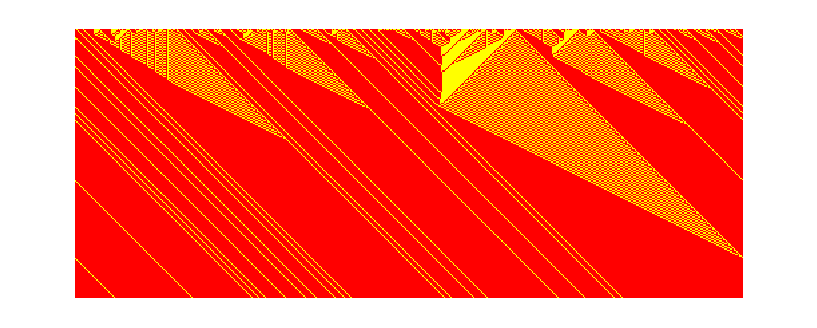

```mathematica
BlockRandom[SeedRandom[567]; 
 ArrayPlot[
  CellularAutomaton[{4196304428, 2, 2}, 
   RandomChoice[{.6, .4} -> {1, 0}, 500], 200], 
  ColorRules -> {0 -> Yellow, 
    1 ->  Red}, Frame -> False]]
```

rule 184: doesn’t achieve consensus on “overall density”, but does do so with respect to left- and right-moving stripes, here with the nested pattern generated when p = 0.5:

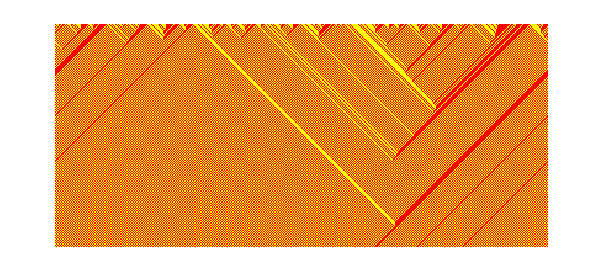

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[184,RandomChoice[{1,0},400],180],ColorRules->{0->Yellow,1->Red},Frame->False]]
```

Achieving consensus faster: comparison of GKL rule with another radius - 3 rule, latter has shorter average consensis time:

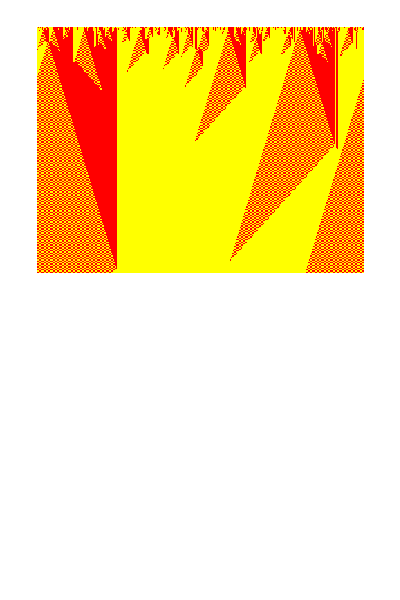

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.48,.52}->{1,0},800],180],ColorRules->{0-> Yellow,1->Red},Frame->False,ImageSize->{650,Automatic}]]&/@{{339789091192587366278221041213531750560,2,3},{339841014953466429132970652455676805280,2,3}}]
```

A more elaborate / ornate way

```mathematica
Column[BlockRandom[SeedRandom[24125];
ArrayPlot[CellularAutomaton[#,RandomChoice[{.48,.52}->{1,0},800],240],ColorRules->{0->Yellow,1->Red},Frame->False,ImageSize->{650,Automatic}]]&/@{{337607298446901146542393000444934784552,2,3},{338557163619953682141694933300561896488,2,3},{313421633154342960352882914658469183496,2,3}}]
```

-Graphics-

Some rules (e.g. optimal sorting rules):  optimal rules will often be ones that don’t look simple in their behavior, and that can’t realistically be constructed by standard engineering methods, 
and essentially just have to be found “experimentally” by searching the computational universe of possible rules.

#### A notable feature in earlier rules

they show a small number of types of very distinct “domains” with definite walls or boundaries between them. And in many ways such walls can be thought of as being like localized structures, “defects” or “particles”

important: whether these particles move around, and whether they annihilate each other to leave a uniform “consensus” final state.

static domain walls exists inevitably in the simple majority rule:

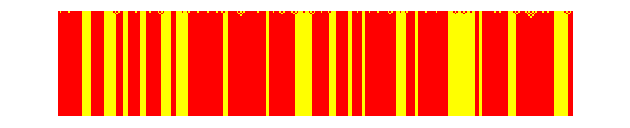

```mathematica
BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[232,RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Yellow,1->Red},MeshStyle->Orange]]
```

A longer range rule that samples more distant cells: With range-2 (i.e. a 5-cell neighborhood) “wrong domains” with widths below 4 disappear:

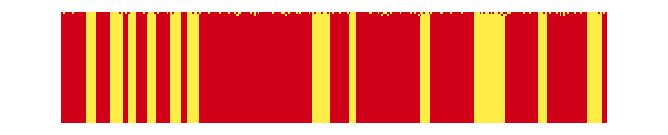

```mathematica
majrn[n_]:=FromDigits[If[Total[#]>n/2,1,0]&/@Tuples[{1,0},n],2]

BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{majrn[5],2,{{-2},{-1},{0},{1},{2}}},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Hue[0.15,0.72,1],1->Hue[0.98,1,0.8200000000000001]},MeshStyle->Orange]]
```

for cells that are non-adjacently sampled, but are for example in the pattern :  no finite-size sampling with the pure majority rule will remove all domains.

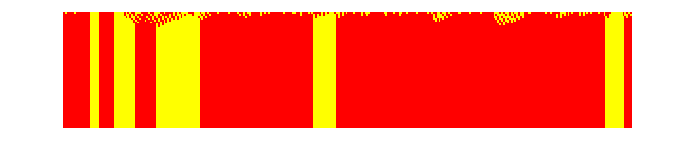

```mathematica
majrn[n_]:=FromDigits[If[Total[#]>n/2,1,0]&/@Tuples[{1,0},n],2]

BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{majrn[5],2,{{-3},{-1},{0},{2},{4}}},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Yellow,1->Red},MeshStyle->Orange]]
```

GKL rule only samples 5 cells, but its “extremities” are at distance  --> “improve” it by having it sample more distant cells
comparing a few cases (the first one is the original):

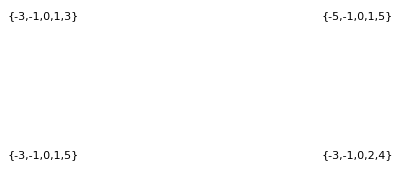

```mathematica
GraphicsGrid[Partition[Labeled[BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{4177065992,2,List/@#},RandomChoice[{.6,.4}->{1,0},300],100],ColorRules->{0->Yellow,1->Red},MeshStyle->Orange,ImageSize->300]],Style[#,11]]&/@{{-3,-1,0,1,3},{-5,-1,0,1,5},{-3,-1,0,1,5},{-3,-1,0,2,4}},2]]
```